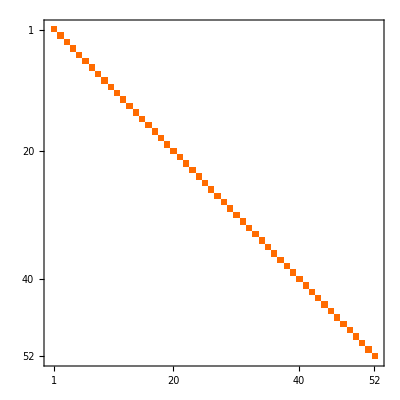
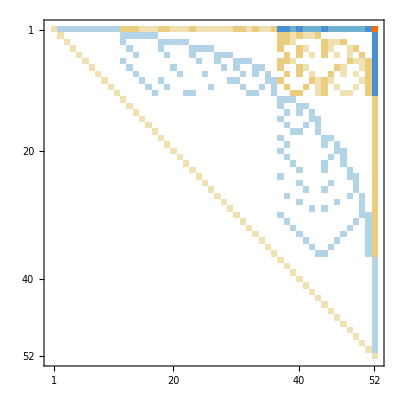
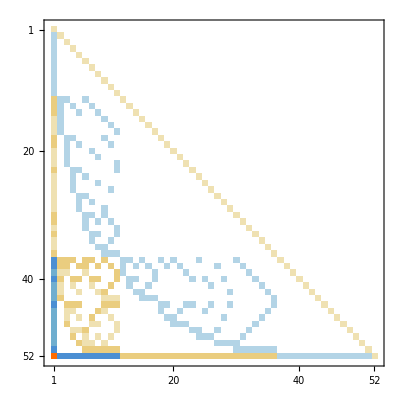
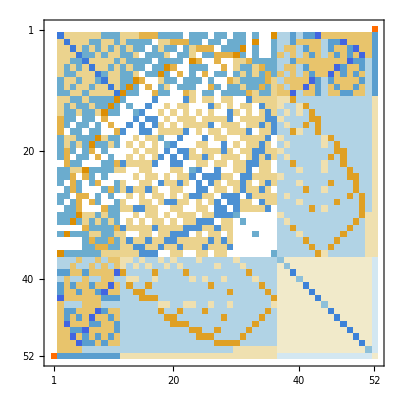
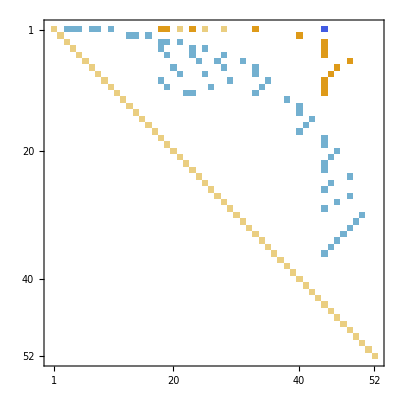
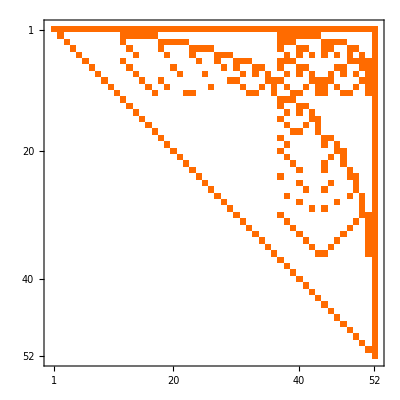
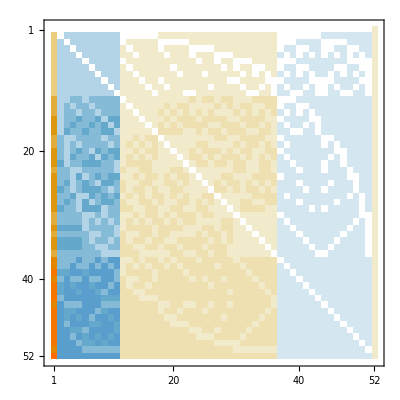
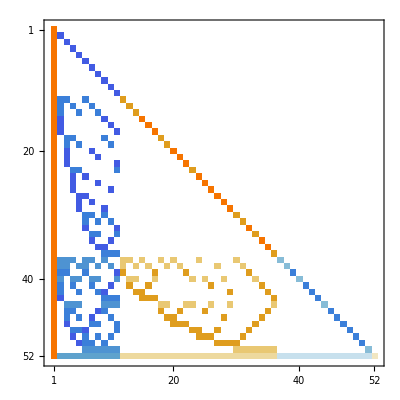
{{-Graphics-C→C,-Graphics-C→E,-Graphics-C→G,-Graphics-C→F,-Graphics-C→T},{-Graphics-E→C,-Graphics-E→E,-Graphics-E→G,-Graphics-E→F,-Graphics-E→T},{-Graphics-G→C,-Graphics-G→E,-Graphics-G→G,-Graphics-G→F,-Graphics-G→T},{-Graphics-F→C,-Graphics-F→E,-Graphics-F→G,-Graphics-F→F,-Graphics-F→T},{-Graphics-T→C,-Graphics-T→E,-Graphics-T→G,-Graphics-T→F,-Graphics-T→T}}

```mathematica
Table[
Labeled[
MatrixPlot[
ConversionMatrix[base1,base2]
],
base1->base2],
{base1,allBases},{base2,allBases}
]
```

```mathematica
ConversionMatrix["E","C"].ConversionMatrix["C","F"]//MatrixPlot
```

-Graphics-

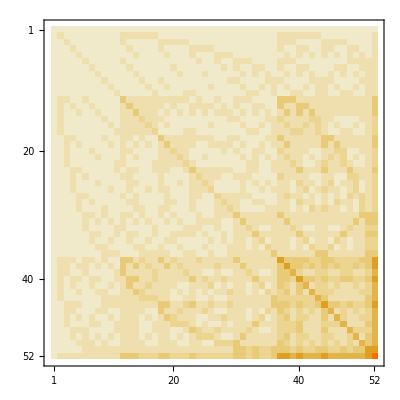

```mathematica
ConversionMatrix["G","C"].ConversionMatrix["E","C"]//MatrixPlot
```

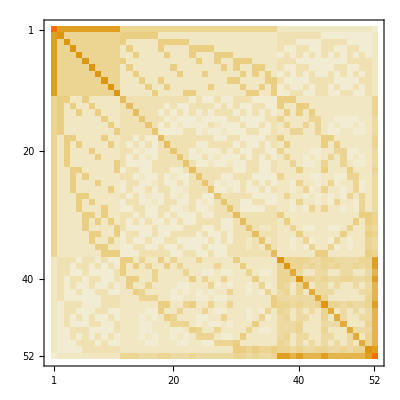

```mathematica
ConversionMatrix["E","C"].ConversionMatrix["G","C"]+ConversionMatrix["G","C"].ConversionMatrix["E","C"]//MatrixPlot
```

```mathematica
ConversionMatrix["E","C"]//Inverse//MatrixPlot
```

-Graphics-

```mathematica
ConversionMatrix["G","C"]*ConversionMatrix["E","C"]//MatrixPlot
```

-Graphics-

```mathematica
ConversionMatrix["G","C"].Inverse[ConversionMatrix["G","C"]]//MatrixPlot
```

-Graphics-

```mathematica
ConversionMatrix["E","C"]==ZetaP[setp5]
```

True

```mathematica
ZetaP[setp8]//MatrixPlot
```

-Graphics-

```mathematica
Table[ZetaP[var]//Flatten//Total,{var,{setp3,setp4,setp5,setp6,setp7}}]
```

{12,60,358,2471,19302}

```mathematica
ConversionMatrix["G","C"]//Flatten//Total
```

358

```mathematica
ConversionMatrix["T","C"]//Flatten//Total
```

```mathematica
131
```

```mathematica
Keys[allGraphs5[1]]
```

{signature,matrix,graph,vertexsets,vertices,edges,relations,links,parents,children,comp,compwhy,colofour,colortable,colofournull,colofourrealnull,atleast,atleastwhy,embed,colofourgenerator,colotree}

```mathematica
Table[Labeled[Length[Select[Flatten[Table[BaseCoeff[k,base],{k,Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&]}]],#==0&]],base],{base,allBases}]
```

{41263C,31816E,46034G,20319F,37071T}

```mathematica
Table[Labeled[Length[Select[Flatten[Table[BaseCoeff[k,base],{k,Keys[allGraphs5]}]],#==0&]],base],{base,allBases}]
```

{82614C,71762E,79774G,39524F,78022T}